```mathematica
alldata=Import[FileNameJoin[{NotebookDirectory[],"fixtures","output.csv"}]];c
```

```mathematica
dataset=Import[FileNameJoin[{NotebookDirectory[],"fixtures","dataset.csv"}]];
```

```mathematica
holidays=DayRange[DateObject[{2014,1,1}],DateObject[{2015,12,31}],"Holiday",HolidayCalendar->{"UnitedStates", "Default"}];
```

```mathematica
extractDataByYear[l_List,y_Integer]:=Select[l,DateValue[First[#],"Year"]==DateValue[{y},"Year"]&]
```

```mathematica
extractDataByWeekday[l_List,w_Symbol]:=
Select[l,DayName[First[#]]==w&]
```

```mathematica
extractHourlyData[l_List]:=Map[Rest,l]
```

```mathematica
plotListWithModel[l_List,nlm_FittedModel]:=Show[Map[ListPlot,l],Plot[nlm[x],{x,0,24}],PlotRange->All,Ticks->{Range[24],Automatic}]
```

```mathematica
getSampleData[l_List,y_Integer,w_Symbol,n_Integer]:=extractHourlyData[extractDataByWeekday[extractDataByYear[dataset,y],w]][[n]]
```

```mathematica
minMaxMeanPlot[y_Integer,w_Symbol]:=ListLinePlot[{Map[Min,Transpose[Map[Rest,extractDataByWeekday[extractDataByYear[dataset,y],w]]]],Map[Max,Transpose[Map[Rest,extractDataByWeekday[extractDataByYear[dataset,y],w]]]],Map[Mean,Transpose[Map[Rest,extractDataByWeekday[extractDataByYear[dataset,y],w]]]]},PlotRange->All,Filling->{1->{2}},Ticks->{Range[1,24],Automatic},GridLines->{Range[1,24],Automatic}]
```

```mathematica
nlm=NonlinearModelFit[getSampleData[dataset,2015,Monday,24],a+b x+c x^2+d x^3+e x^4,{a,b,c,d,e},x]
```

FittedModel[1110.41-1073.15 x+255.375 x^2-16.7501 x^3+0.329474 x^4]

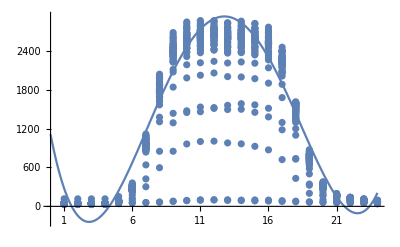

```mathematica
plotListWithModel[extractHourlyData[extractDataByWeekday[extractDataByYear[dataset,2015],Monday]],nlm]
```

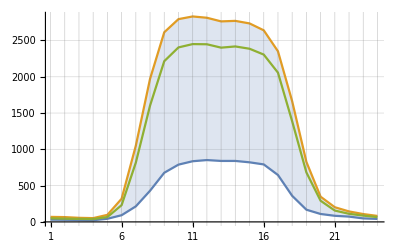

```mathematica
minMaxMeanPlot[2014,Tuesday]
```

```mathematica
(*Extract all data in mondays which max numbers of parking cars is greater than 2000*)
```

```mathematica
selectedMondays=DateObject[DateList[First[#]][[1;;3]]]&/@Select[extractDataByWeekday[dataset,Monday],Max[Rest[#]]>2000&];
```

```mathematica
trainingdataBiased={DateValue[#1,"Hour"]}->#2&@@@Select[alldata,MemberQ[selectedMondays,DateObject[DateList[First[#]][[1;;3]]]]&];
```

```mathematica
pBiased=Predict[trainingdataBiased]
```

PredictorFunction[…]

```mathematica
(*Extract all data in mondays*)
trainingdataUnbiased={DateValue[#1,"Hour"],MemberQ[holidays,DateObject[DateList[#1][[1;;3]]]]}->#2&@@@Select[alldata,(DateValue[First[#],"Year"]==DateValue[{2014},"Year"]|| DateValue[First[#],"Year"]==DateValue[{2015},"Year"])&&DayName[First[#]]==Monday&]
```

{{0,False}→22,{1,False}→17,{2,False}→16,{4,False}→39,{5,False}→186,{6,False}→749,{3,False}→15,{7,False}→1529,{8,False}→2160,{9,False}→2316,{10,False}→2363,{11,False}→2394,{12,False}→2363,{13,False}→2359,2468,{10,False}→1001,{11,False}→1007,{12,False}→979,{13,False}→965,{14,False}→927,{15,False}→872,{16,False}→722,{17,False}→432,{18,False}→201,{19,False}→103,{20,False}→68,{21,False}→59,{22,False}→48,{23,False}→40}
 |  |  |  |

```mathematica
pUnbiased=Predict[trainingdataUnbiased,Method->"RandomForest"]
```

PredictorFunction[…]

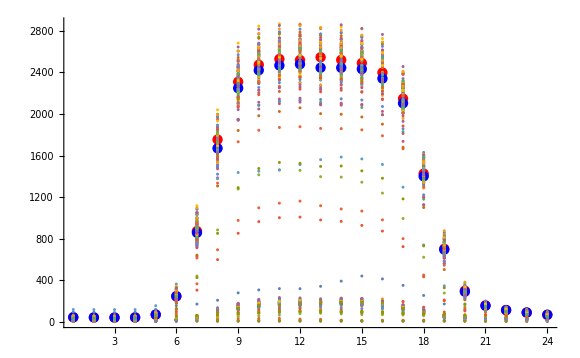

```mathematica
Show[ListPlot[Map[pBiased,Range[0,23]],PlotStyle->Red],ListPlot[Map[pUnbiased,{#,False}&/@Range[0,23]],PlotStyle->Blue],ListPlot[Map[Rest,extractDataByWeekday[dataset,Monday]]],PlotRange->All]
```

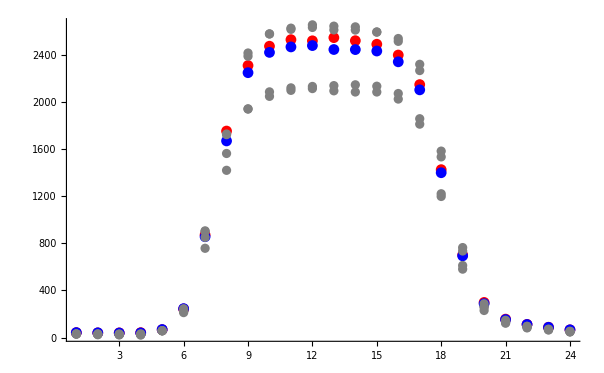

```mathematica
Show[ListPlot[Map[pBiased,Range[0,23]],PlotStyle->Red],ListPlot[Map[pUnbiased,{#,False}&/@Range[0,23]],PlotStyle->Blue],ListPlot[Map[Rest,extractDataByWeekday[extractDataByYear[dataset,2016],Monday]],PlotStyle->Gray],PlotRange->All]
```

```mathematica
data1415=Select[alldata,DateValue[First[#],"Year"]==DateValue[{2014},"Year"]||DateValue[First[#],"Year"]==DateValue[{2015},"Year"]&];
```

```mathematica
selectedTuesdays=DateObject[DateList[First[#]][[1;;3]]]&/@Select[extractDataByWeekday[Join[extractDataByYear[dataset,2014],extractDataByYear[dataset,2015]],Tuesday],Max[Rest[#]]>2000&];
```

```mathematica
trainingdataTuesday={DateValue[#1,"Hour"]}->#2&@@@Select[data1415,MemberQ[selectedTuesdays,DateObject[DateList[First[#]][[1;;3]]]]&];
```

```mathematica
pTuesday=Predict[trainingdataTuesday,Method->"RandomForest"]
```

PredictorFunction[…]

```mathematica
selectedWednesday=DateObject[DateList[First[#]][[1;;3]]]&/@Select[extractDataByWeekday[Join[extractDataByYear[dataset,2014],extractDataByYear[dataset,2015]],Wednesday],Max[Rest[#]]>2000&];
```

```mathematica
trainingdataWednesday={DateValue[#1,"Hour"]}->#2&@@@Select[data1415,MemberQ[selectedWednesday,DateObject[DateList[First[#]][[1;;3]]]]&];
```

```mathematica
pWednesday=Predict[trainingdataWednesday,Method->"RandomForest"]
```

PredictorFunction[…]

```mathematica
selectedThursday=DateObject[DateList[First[#]][[1;;3]]]&/@Select[extractDataByWeekday[Join[extractDataByYear[dataset,2014],extractDataByYear[dataset,2015]],Thursday],Max[Rest[#]]>2000&];
```

```mathematica
trainingdataThursday={DateValue[#1,"Hour"]}->#2&@@@Select[data1415,MemberQ[selectedThursday,DateObject[DateList[First[#]][[1;;3]]]]&];
```

```mathematica
pThursday=Predict[trainingdataThursday,Method->"RandomForest"]
```

PredictorFunction[…]

```mathematica
selectedFriday=DateObject[DateList[First[#]][[1;;3]]]&/@Select[extractDataByWeekday[Join[extractDataByYear[dataset,2014],extractDataByYear[dataset,2015]],Friday],Max[Rest[#]]>1600&];
```

```mathematica
trainingdataFriday={DateValue[#1,"Hour"]}->#2&@@@Select[data1415,MemberQ[selectedFriday,DateObject[DateList[First[#]][[1;;3]]]]&];
```

```mathematica
pFriday=Predict[trainingdataFriday,Method->"RandomForest"]
```

PredictorFunction[…]

```mathematica
selectedSaturday=DateObject[DateList[First[#]][[1;;3]]]&/@Select[extractDataByWeekday[Join[extractDataByYear[dataset,2014],extractDataByYear[dataset,2015]],Saturday],Max[Rest[#]]<145&];
```

```mathematica
trainingdataSaturday={DateValue[#1,"Hour"]}->#2&@@@Select[data1415,MemberQ[selectedSaturday,DateObject[DateList[First[#]][[1;;3]]]]&];
```

```mathematica
pSaturday=Predict[trainingdataSaturday,Method->"RandomForest"]
```

PredictorFunction[…]

```mathematica
selectedSunday=DateObject[DateList[First[#]][[1;;3]]]&/@Select[extractDataByWeekday[Join[extractDataByYear[dataset,2014],extractDataByYear[dataset,2015]],Sunday],Max[Rest[#]]<155&];
```

```mathematica
trainingdataSunday={DateValue[#1,"Hour"]}->#2&@@@Select[data1415,MemberQ[selectedSunday,DateObject[DateList[First[#]][[1;;3]]]]&];
```

```mathematica
pSunday=Predict[trainingdataSunday,Method->"RandomForest"]
```

PredictorFunction[…]

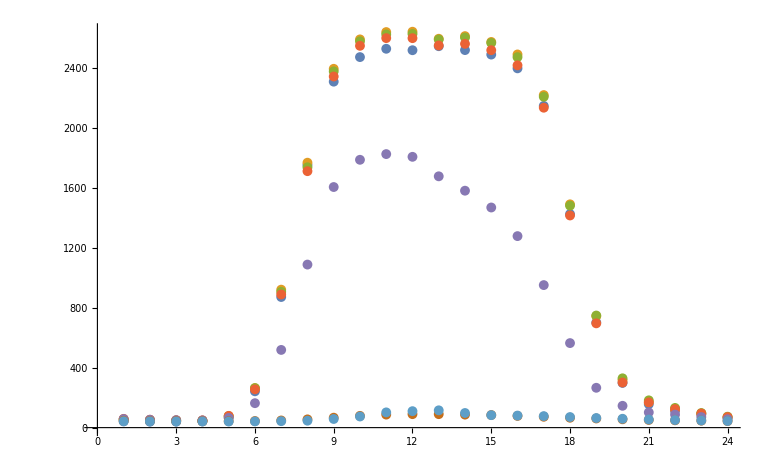

```mathematica
Show[ListPlot[{Map[pBiased,Range[0,23]],Map[pTuesday,Range[0,23]],Map[pWednesday,Range[0,23]],Map[pThursday,Range[0,23]],Map[pFriday,Range[0,23]],Map[pSaturday,Range[0,23]],Map[pSunday,Range[0,23]]}]]
```

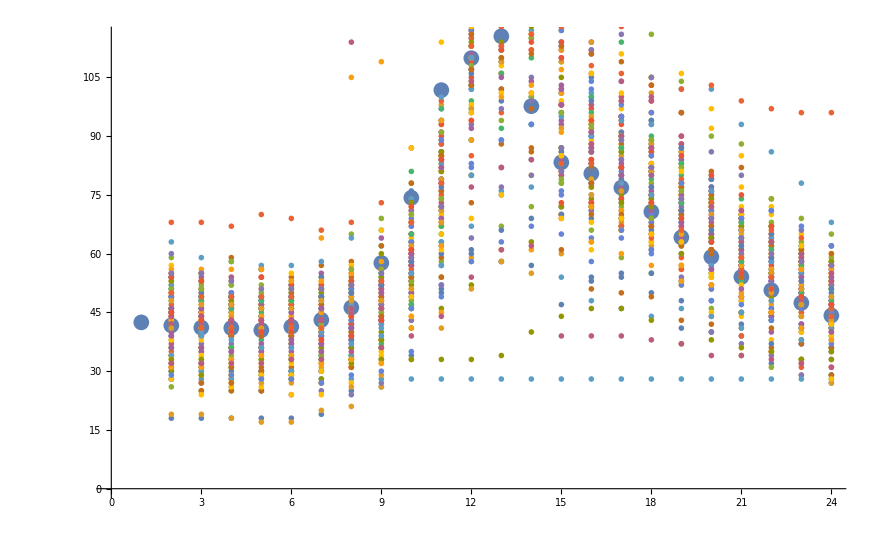

```mathematica
Show[ListPlot[Map[pSunday,Range[0,23]]],ListPlot[extractDataByWeekday[Join[extractDataByYear[dataset,2014],extractDataByYear[dataset,2015]],Sunday]]]
```

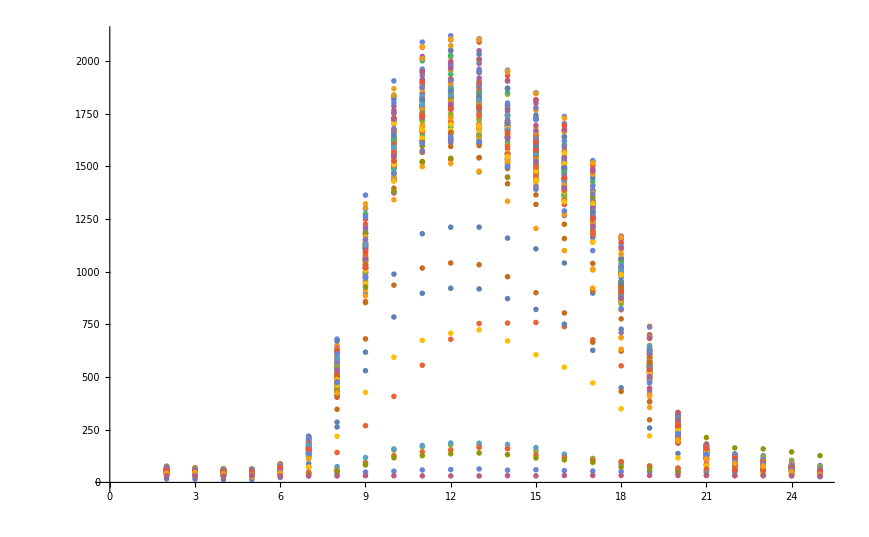

```mathematica
ListPlot[extractDataByWeekday[Join[extractDataByYear[dataset,2014],extractDataByYear[dataset,2015]],Friday]]
```

```mathematica
Map[pTuesday,Range[0,23]]
```

{53.1312,47.9736,45.2483,43.6975,75.2631,264.136,921.057,1768.75,2395.57,2591.86,2640.81,2643.11,2596.18,2613.81,2574.84,2491.35,2220.16,1490.81,744.168,317.193,169.525,122.142,93.7386,70.0586}

```mathematica
Map[Rest,extractDataByWeekday[extractDataByYear[dataset,2016],Tuesday]]
```

{{37,32,29,30,62,244,824,1607,2182,2375,2417,2426,2366,2359,2320,2236,1995,1328,607,234,125,91,70,56},{46,38,30,32,63,260,938,1840,2481,2678,2746,2761,2748,2770,2733,2639,2372,1666,877,405,270,210,186,167},{38,36,35,30,62,255,935,1746,2373,2601,2647,2676,2630,2651,2611,2541,2284,1597,833,323,175,121,84,64},{38,34,23,21,53,261,936,1792,2473,2674,2719,2692,2639,2651,2635,2570,2336,1605,809,303,140,94,69,47}}

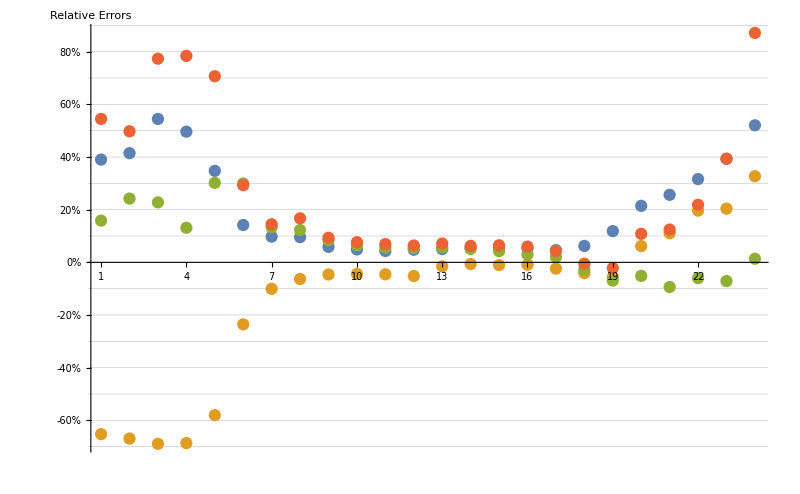

```mathematica
ListPlot[100*(Subtract[Map[pWednesday,Range[0,23]],#]/#)&/@Map[Rest,extractDataByWeekday[extractDataByYear[dataset,2016],Wednesday]],AxesLabel->"Relative Errors",Ticks->{Range[1,24],{#,ToString[#]<>"%"}&/@Range[-100,100,10]},GridLines->{None,Range[-100,100,10]}, PlotRange->All]
```

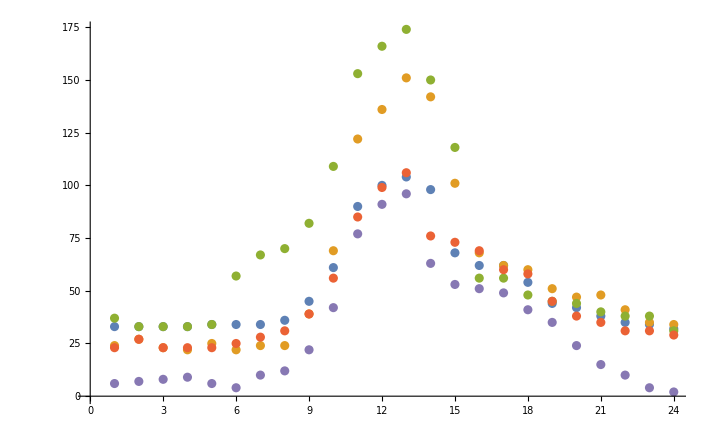

```mathematica
ListPlot[Map[Rest,extractDataByWeekday[extractDataByYear[dataset,2016],Sunday]]]
```

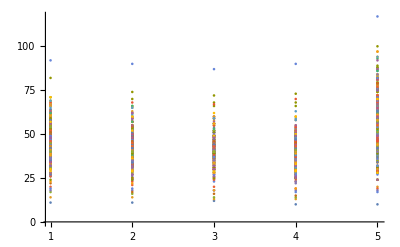

```mathematica
ListPlot[Take[#,5]&/@Map[Rest,Select[dataset,DateValue[First[#],"Year"]==DateValue[{2014},"Year"]&]],PlotRange->All]
```

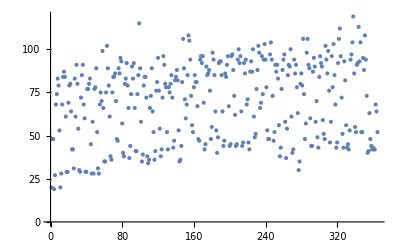

```mathematica
ListPlot[Max[Take[#,-2]]&/@Map[Rest,Select[dataset,DateValue[First[#],"Year"]==DateValue[{2014},"Year"]&]],PlotRange->All]
```

```mathematica
Max[Take[#,-2]]&/@Map[Rest,Select[dataset,DateValue[First[#],"Year"]==DateValue[{2014},"Year"]&]]
```

{20,48,48,19,27,68,74,83,79,53,20,28,68,84,87,84,61,29,29,69,79,80,64,42,42,31,83,61,91,80,54,30,29,72,85,91,68,60,29,29,77,77,80,83,45,28,58,28,77,78,89,52,31,28,68,75,70,99,66,35,35,75,102,89,79,61,38,36,75,84,84,86,70,48,47,89,86,95,93,57,40,38,80,83,92,79,66,37,44,74,90,83,92,66,41,41,74,85,115,89,58,35,39,79,84,84,72,38,34,36,66,73,89,64,52,36,41,76,81,95,76,54,38,42,72,96,91,80,78,52,42,78,75,80,85,72,43,47,82,84,88,82,53,35,36,44,81,106,89,71,60,68,85,108,105,94,73,56,52,78,85,81,81,67,48,47,94,96,92,96,69,42,45,90,85,86,88,76,48,55,98,94,85,64,53,40,49,92,93,93,85,64,44,47,86,84,91,96,67,44,45,96,97,88,73,62,44,45,94,100,92,96,64,44,46,92,86,94,68,71,46,42,87,93,87,100,61,49,51,77,88,102,98,66,69,96,74,94,103,94,78,53,48,48,97,104,94,73,47,52,91,87,91,83,56,38,43,77,88,94,97,58,37,54,85,91,90,100,61,40,42,94,86,91,78,63,30,35,80,86,79,106,74,48,57,98,106,91,89,60,44,44,87,95,90,58,70,49,43,84,96,92,90,59,51,48,102,94,86,99,76,46,58,96,78,103,85,68,43,46,92,106,112,96,72,51,43,93,82,56,43,45,42,53,94,97,104,119,86,55,52,91,92,113,93,104,52,52,95,88,108,94,73,40,41,63,48,44,42,43,42,42,68,64,52}

```mathematica
Accumulate[Flatten[Subtract[Map[pWednesday,Range[0,23]],#]&/@Map[Rest,extractDataByWeekday[extractDataByYear[dataset,2016],Wednesday]]]]
```

{15.6102,30.5359,47.419,62.8037,82.6107,115.368,195.961,347.911,480.038,600.219,709.169,829.224,953.178,1090.47,1221.72,1346.05,1443.85,1530.79,1610.12,1668.3,1705.49,1737.1,1764.64,1789.62,1685.23,1582.15,1476.04,1374.42,1268.23,1186.99,1085.58,968.529,853.656,734.837,609.787,465.842,425.796,409.088,382.334,359.667,305.468,242.404,197.734,216.918,235.103,256.72,273.255,291.235,298.845,308.771,317.654,323.039,340.846,401.603,508.197,698.147,883.274,1040.45,1179.4,1315.46,1454.41,1580.71,1685.95,1757.28,1801.09,1757.02,1701.35,1683.54,1664.72,1656.34,1648.87,1649.85,1669.46,1686.39,1707.27,1727.66,1759.46,1819.22,1933.81,2182.76,2385.89,2569.07,2739.02,2897.08,3070.03,3223.32,3379.57,3518.9,3609.7,3601.64,3584.97,3617.15,3637.34,3660.96,3688.49,3722.47}

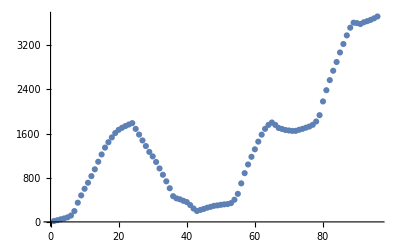

```mathematica
ListPlot[Accumulate[Flatten[Subtract[Map[pWednesday,Range[0,23]],#]&/@Map[Rest,extractDataByWeekday[extractDataByYear[dataset,2016],Wednesday]]]]]
```

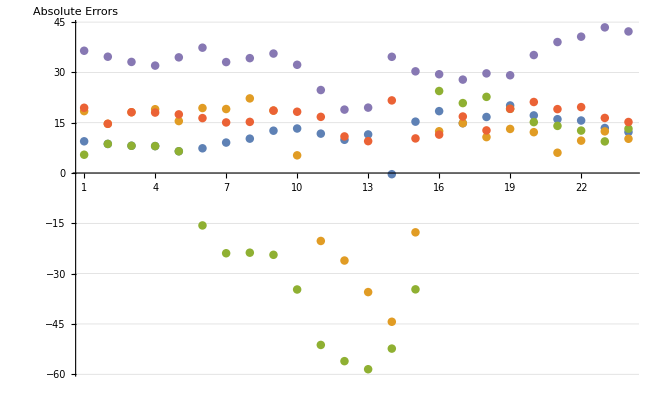

```mathematica
ListPlot[Subtract[Map[pSunday,Range[0,23]],#]&/@Map[Rest,extractDataByWeekday[extractDataByYear[dataset,2016],Sunday]],AxesLabel->"Absolute Errors",Ticks->{Range[1,24],Automatic},GridLines->{None,Automatic}, PlotRange->All]
```

```mathematica
(*From previous view, We can learn from that Peak period the absolute error is great but relative error is small. But in off-peak period relative error is high but absolute error is small.*)
```

```mathematica
DatePlus[#,1]&/@holidays
```

{Thu 2 Jan 2014,Tue 21 Jan 2014,Tue 18 Feb 2014,Tue 27 May 2014,Sat 5 Jul 2014,Tue 2 Sep 2014,Tue 14 Oct 2014,Wed 12 Nov 2014,Fri 28 Nov 2014,Fri 26 Dec 2014,Fri 2 Jan 2015,Tue 20 Jan 2015,Tue 17 Feb 2015,Tue 26 May 2015,Sat 4 Jul 2015,Tue 8 Sep 2015,Tue 13 Oct 2015,Thu 12 Nov 2015,Fri 27 Nov 2015,Sat 26 Dec 2015}

```mathematica
DatePlus[#,-1]&/@holidays
```

```mathematica
holidayss=Join[holidays,DatePlus[#,1]&/@holidays,DatePlus[#,-1]&/@holidays]
```

{Wed 1 Jan 2014,Mon 20 Jan 2014,Mon 17 Feb 2014,Mon 26 May 2014,Fri 4 Jul 2014,Mon 1 Sep 2014,Mon 13 Oct 2014,Tue 11 Nov 2014,Thu 27 Nov 2014,Thu 25 Dec 2014,Thu 1 Jan 2015,Mon 19 Jan 2015,Mon 16 Feb 2015,Mon 25 May 2015,Fri 3 Jul 2015,Mon 7 Sep 2015,Mon 12 Oct 2015,Wed 11 Nov 2015,Thu 26 Nov 2015,Fri 25 Dec 2015,Thu 2 Jan 2014,Tue 21 Jan 2014,Tue 18 Feb 2014,Tue 27 May 2014,Sat 5 Jul 2014,Tue 2 Sep 2014,Tue 14 Oct 2014,Wed 12 Nov 2014,Fri 28 Nov 2014,Fri 26 Dec 2014,Fri 2 Jan 2015,Tue 20 Jan 2015,Tue 17 Feb 2015,Tue 26 May 2015,Sat 4 Jul 2015,Tue 8 Sep 2015,Tue 13 Oct 2015,Thu 12 Nov 2015,Fri 27 Nov 2015,Sat 26 Dec 2015,Tue 31 Dec 2013,Sun 19 Jan 2014,Sun 16 Feb 2014,Sun 25 May 2014,Thu 3 Jul 2014,Sun 31 Aug 2014,Sun 12 Oct 2014,Mon 10 Nov 2014,Wed 26 Nov 2014,Wed 24 Dec 2014,Wed 31 Dec 2014,Sun 18 Jan 2015,Sun 15 Feb 2015,Sun 24 May 2015,Thu 2 Jul 2015,Sun 6 Sep 2015,Sun 11 Oct 2015,Tue 10 Nov 2015,Wed 25 Nov 2015,Thu 24 Dec 2015}

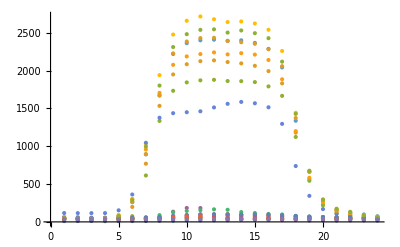

```mathematica
ListPlot[Map[Rest,Select[dataset,MemberQ[holidays,DateObject[DateList[First[#]][[1;;3]]]]&]]]
```

```mathematica
Select[dataset,MemberQ[holidays,DateObject[DateList[First[#]][[1;;3]]]]&]//TableForm
```

2014-01-01 00:00:00 | 11 | 11 | 12 | 10 | 10 | 11 | 12 | 15 | 16 | 19 | 20 | 22 | 23 | 30 | 28 | 27 | 24 | 26 | 19 | 19 | 18 | 20 | 20 | 17
2014-01-20 00:00:00 | 27 | 26 | 24 | 22 | 49 | 198 | 769 | 1533 | 1948 | 2083 | 2123 | 2134 | 2112 | 2094 | 2062 | 1992 | 1830 | 1179 | 562 | 231 | 129 | 92 | 69 | 43
2014-02-17 00:00:00 | 28 | 28 | 28 | 28 | 34 | 76 | 613 | 1334 | 1732 | 1843 | 1870 | 1877 | 1861 | 1859 | 1847 | 1790 | 1665 | 1122 | 543 | 218 | 110 | 74 | 58 | 46
2014-05-26 00:00:00 | 34 | 32 | 30 | 29 | 29 | 29 | 31 | 40 | 48 | 57 | 63 | 77 | 81 | 75 | 68 | 67 | 64 | 62 | 52 | 50 | 48 | 45 | 43 | 44
2014-07-04 00:00:00 | 45 | 40 | 40 | 40 | 40 | 41 | 42 | 49 | 53 | 59 | 61 | 64 | 58 | 60 | 56 | 54 | 52 | 51 | 49 | 50 | 54 | 55 | 53 | 44
2014-09-01 00:00:00 | 45 | 44 | 43 | 45 | 42 | 42 | 45 | 49 | 65 | 79 | 93 | 95 | 102 | 95 | 96 | 89 | 77 | 75 | 68 | 63 | 59 | 56 | 48 | 46
2014-10-13 00:00:00 | 48 | 44 | 41 | 43 | 75 | 260 | 892 | 1670 | 2218 | 2361 | 2399 | 2407 | 2392 | 2399 | 2365 | 2286 | 2041 | 1336 | 663 | 286 | 163 | 124 | 98 | 75
2014-11-11 00:00:00 | 69 | 66 | 56 | 51 | 93 | 301 | 1031 | 1939 | 2475 | 2657 | 2714 | 2677 | 2640 | 2648 | 2621 | 2538 | 2258 | 1442 | 664 | 269 | 163 | 113 | 78 | 61
2014-11-27 00:00:00 | 42 | 40 | 41 | 42 | 42 | 43 | 48 | 60 | 135 | 184 | 183 | 68 | 45 | 44 | 44 | 44 | 42 | 45 | 45 | 43 | 42 | 42 | 43 | 43
2014-12-25 00:00:00 | 42 | 42 | 42 | 44 | 42 | 42 | 42 | 41 | 43 | 43 | 43 | 45 | 42 | 40 | 40 | 39 | 39 | 39 | 41 | 41 | 40 | 40 | 40 | 42
2015-01-01 00:00:00 | 51 | 48 | 47 | 47 | 49 | 50 | 50 | 51 | 50 | 54 | 55 | 53 | 50 | 39 | 40 | 41 | 43 | 44 | 40 | 42 | 40 | 41 | 38 | 38
2015-01-19 00:00:00 | 117 | 116 | 116 | 116 | 153 | 362 | 1045 | 1376 | 1436 | 1449 | 1461 | 1512 | 1560 | 1585 | 1567 | 1514 | 1295 | 738 | 344 | 169 | 105 | 83 | 67 | 49
2015-02-16 00:00:00 | 43 | 43 | 40 | 40 | 76 | 300 | 956 | 1704 | 2075 | 2186 | 2217 | 2239 | 2213 | 2229 | 2210 | 2139 | 1884 | 1199 | 583 | 265 | 149 | 107 | 85 | 67
2015-05-25 00:00:00 | 51 | 51 | 50 | 50 | 52 | 53 | 59 | 65 | 76 | 87 | 94 | 99 | 92 | 89 | 84 | 82 | 76 | 71 | 65 | 62 | 61 | 50 | 51 | 48
2015-07-03 00:00:00 | 54 | 54 | 50 | 47 | 46 | 47 | 55 | 89 | 127 | 145 | 154 | 166 | 160 | 130 | 117 | 105 | 98 | 77 | 68 | 64 | 58 | 60 | 57 | 53
2015-09-07 00:00:00 | 54 | 54 | 54 | 56 | 57 | 56 | 58 | 66 | 80 | 92 | 101 | 102 | 102 | 96 | 99 | 97 | 88 | 80 | 71 | 65 | 59 | 60 | 56 | 54
2015-10-12 00:00:00 | 47 | 43 | 42 | 46 | 75 | 262 | 896 | 1671 | 2226 | 2383 | 2428 | 2432 | 2390 | 2373 | 2353 | 2281 | 2057 | 1372 | 661 | 286 | 151 | 117 | 86 | 67
2015-11-11 00:00:00 | 43 | 37 | 34 | 36 | 78 | 284 | 995 | 1801 | 2310 | 2480 | 2537 | 2544 | 2501 | 2529 | 2493 | 2427 | 2117 | 1427 | 676 | 297 | 174 | 133 | 83 | 59
2015-11-26 00:00:00 | 36 | 38 | 34 | 38 | 35 | 37 | 36 | 34 | 61 | 74 | 76 | 37 | 35 | 34 | 35 | 37 | 36 | 36 | 37 | 36 | 34 | 35 | 35 | 33
2015-12-25 00:00:00 | 31 | 31 | 30 | 34 | 30 | 30 | 31 | 32 | 32 | 31 | 31 | 31 | 32 | 31 | 33 | 33 | 33 | 33 | 33 | 33 | 32 | 32 | 31 | 30